# Projektna naloga za računalniška orodja v matematiki

5.7.2025

Uvod
V projektu analiziramo gibanje cen osnovnih živil v Sloveniji, s poudarkom na kruhu, mesu, mleku in sadju. Namen analize je razumeti, kako se cene spreminjajo skozi čas in kakšen vpliv imajo ti premiki na potrošnike in trg. Posebna pozornost je namenjena inflaciji, letnim spremembam ter relativni rasti cen posameznih živil, kar omogoča celostno sliko ekonomskih in družbenih vplivov. Za vizualizacijo in analizo podatkov uporabljam programsko okolje Mathematica, ki omogoča učinkovito obdelavo in predstavitev rezultatov.

Metodologija
Podatki o cenah osnovnih živil (kruh, meso, mleko, sadje) so bili pridobljeni iz spletne baze Statističnega urada Republike Slovenije (SURS), natančneje s portala SiStat (https://pxweb.stat.si/SiStatData/pxweb/sl/Data/-/0411005S.px). Ti podatki zajemajo letne cene živil v Sloveniji za obdobje [2018–2024].
Uporabila sem različne metode za izračun:
Letne absolutne in procentualne spremembe cen,
Skupno vrednost cen živil v posameznem letu,
Normalizacijo cen za prikaz relativne rasti,
Vizualizacije kot so stolpčni diagrami, črtni grafi in tortni diagrami.
Pri analizi sem uporabila funkcije Map, MapThread, Grid ter ListLinePlot, BarChart in PieChart, ki nomogram učinkovito predstavitev podatkov in izpostavitev ključnih trendov.

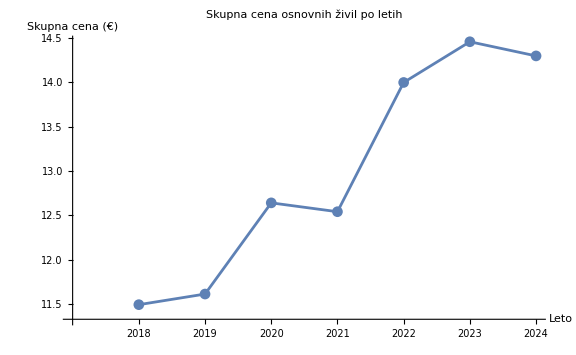

```mathematica
(*Podatki*)leta={2018,2019,2020,2021,2022,2023,2024};

kruh={2.13,2.27,2.42,2.37,2.87,3.30,3.42};
meso={7.27,7.47,7.92,7.98,8.62,8.55,8.27};
mleko={0.74,0.74,0.77,0.76,1.00,1.16,1.12};
sadje={1.35,1.13,1.53,1.43,1.51,1.45,1.49};

(*Ta graf prikazuje skupno vrednost cen osnovnih živil–kruha,mesa,mleka in sadja–po posameznih letih.Poudarja,kako se je skozi čas spreminjal finančni pritisk na gospodinjstva zaradi osnovnih živil.Vizualizacija omogoča boljše razumevanje cenovne dinamike ter njenega vpliva na potrošnike in življenjske stroške.*)

ListLinePlot[skupnaCena,PlotLabel->"Skupna cena osnovnih živil po letih",AxesLabel->{"Leto","Skupna cena (€)"},Ticks->{Table[{i,leta[[i]]},{i,Length[leta]}],Automatic},PlotMarkers->Automatic,ImageSize->Large]
```

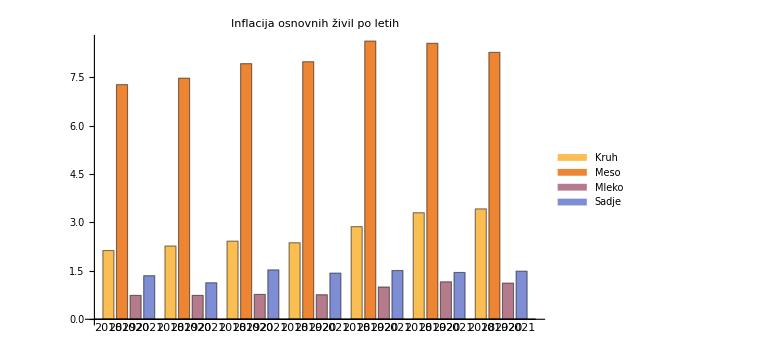

```mathematica
(*Graf prikazuje letne spremembe cen kruha,mesa,mleka in sadja.Vidni so različni trendi,ki kažejo,da se cene posameznih živil ne spreminjajo enakomerno.To odraža raznolike dejavnike,ki vplivajo na proizvodnjo,povpraševanje in trg posameznih živil.*)
BarChart[Transpose@{kruh,meso,mleko,sadje},ChartLabels->Placed[leta,Below],ChartLegends->{"Kruh","Meso","Mleko","Sadje"},PlotLabel->"Inflacija osnovnih živil po letih",ImageSize->Large]
```

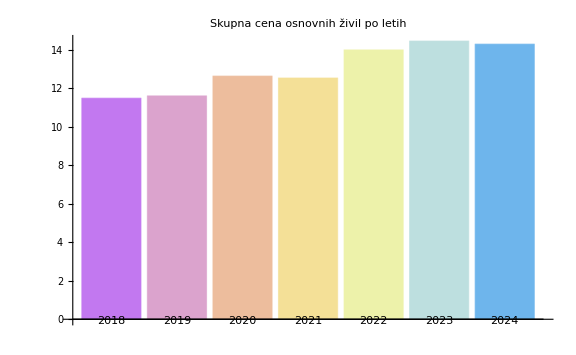

```mathematica
(*Stolpčni graf prikazuje skupno ceno vseh osnovnih živil po letih. Opazen je trend rasti,kar kaže na naraščajoč finančni pritisk na gospodinjstva.*)
BarChart[skupnaCena,ChartLabels->leta,PlotLabel->"Skupna cena osnovnih živil po letih",ChartStyle->"Pastel",ImageSize->Large]
```

```mathematica
(*Tortni diagram prikazuje razmerje med cenami kruha,mesa,mleka in sadja v letu 2024. Vizualno izpostavi,katero živilo prispeva največ k skupni vrednosti osnovnih živil in tako pomaga razumeti strukturo potrošniške košarice v tem obdobju.*)
PieChart[{kruh[[-1]],meso[[-1]],mleko[[-1]],sadje[[-1]]},ChartLegends->{"Kruh","Meso","Mleko","Sadje"},PlotLabel->"Delež cen posameznih živil (2024)",ChartStyle->"BrightPastel"]
```

ColorData::notent: BrightPastel is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

-Graphics-

```mathematica
(*Tabela prikazuje letne cene kruha,mesa,mleka in sadja ter skupno ceno za vsa živila.Omogoča pregledno primerjavo in analizo gibanja cen skozi čas.*)
cenovnaTabela=Grid[Prepend[Transpose@{leta,kruh,meso,mleko,sadje,skupnaCena},{"Leto","Kruh (€)","Meso (€)","Mleko (€)","Sadje (€)","Skupna Cena (€)"}],Frame->All,Background->{None,{{LightGray}}},Alignment->Center]
```

Leto | Kruh (€) | Meso (€) | Mleko (€) | Sadje (€) | Skupna Cena (€)
2018 | 2.13 | 7.27 | 0.74 | 1.35 | 11.49
2019 | 2.27 | 7.47 | 0.74 | 1.13 | 11.61
2020 | 2.42 | 7.92 | 0.77 | 1.53 | 12.64
2021 | 2.37 | 7.98 | 0.76 | 1.43 | 12.54
2022 | 2.87 | 8.62 | 1. | 1.51 | 14.
2023 | 3.3 | 8.55 | 1.16 | 1.45 | 14.46
2024 | 3.42 | 8.27 | 1.12 | 1.49 | 14.3

```mathematica
(*Tabela prikazuje letne odstotne spremembe cen kruha,mesa,mleka,sadja in skupne cene.Omogoča hitro prepoznavanje obdobij večjih rastov ali padcev ter analizo dinamike cen skozi čas*)
pctChange[data_]:=Prepend[Round[Differences[data]/Most[data]*100,0.1],Null];

spremembeTabela=Grid[Prepend[Transpose@{leta,pctChange[kruh],pctChange[meso],pctChange[mleko],pctChange[sadje],pctChange[skupnaCena]},{"Leto","Kruh (%)","Meso (%)","Mleko (%)","Sadje (%)","Skupaj (%)"}],Frame->All,Background->{None,{{LightGray}}},Alignment->Center]
```

Leto | Kruh (%) | Meso (%) | Mleko (%) | Sadje (%) | Skupaj (%)
2018 |  |  |  |  | 
2019 | 6.6 | 2.8 | 0. | -16.3 | 1.
2020 | 6.6 | 6. | 4.1 | 35.4 | 8.9
2021 | -2.1 | 0.8 | -1.3 | -6.5 | -0.8
2022 | 21.1 | 8. | 31.6 | 5.6 | 11.6
2023 | 15. | -0.8 | 16. | -4. | 3.3
2024 | 3.6 | -3.3 | -3.4 | 2.8 | -1.1

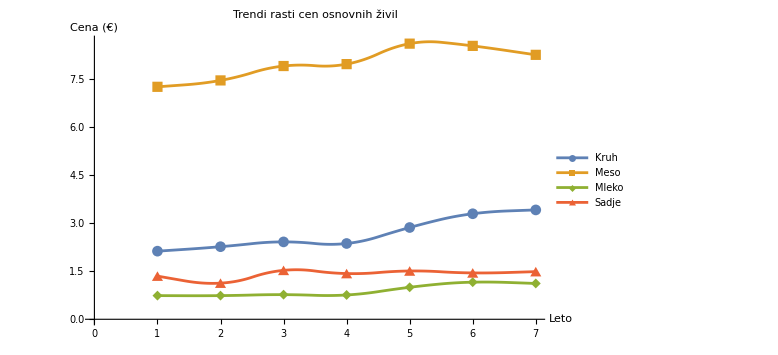

```mathematica
(*Črtni diagram prikazuje razvoj cen kruha,mesa,mleka in sadja skozi čas.Ta vizualizacija omogoča bolj gladek in pregleden vpogled v trende,saj izpostavi tako dolgoročne vzorce kot tudi manjše nihaje.*)
ListLinePlot[{kruh,meso,mleko,sadje},PlotLegends->{"Kruh","Meso","Mleko","Sadje"},PlotLabel->"Trendi rasti cen osnovnih živil",AxesLabel->{"Leto","Cena (€)"},PlotMarkers->Automatic,InterpolationOrder->2,ImageSize->Large]
```

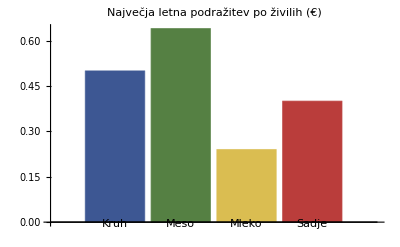

```mathematica
(*Graf prikazuje največje enolete povečave cen za posamezno živilo v obdobju analize.Stolpci jasno izpostavijo,katera živila so bila najbolj podvržena nenadnim in izrazitim podražitvam,kar je pomemben pokazatelj njihove cenovne občutljivosti.*)
maxSkoki=Map[Function[data,Max[Differences[data]]],{kruh,meso,mleko,sadje}];

BarChart[maxSkoki,ChartLabels->{"Kruh","Meso","Mleko","Sadje"},PlotLabel->"Največja letna podražitev po živilih (€)",ChartStyle->"DarkRainbow"]
```

Zaključek
V tej analizi smo skozi grafične prikaze in tabelarične preglede raziskali gibanje cen osnovnih živil – kruha, mesa, mleka in sadja – v Sloveniji v zadnjih letih. Ugotovili smo, da se cene posameznih živil ne spreminjajo enakomerno, kar odraža kompleksnost dejavnikov, ki vplivajo na njihovo oblikovanje. Med temi dejavniki izstopajo globalni vplivi, kot so inflacija, vremenske spremembe, pa tudi lokalni tržni pogoji in proizvodni stroški.

Z analizo absolutnih cen in njihovih letnih sprememb smo opazili, da so nekatera živila doživela izrazite skoke cen, ki lahko močno obremenijo potrošnike, zlasti ranljive skupine prebivalstva. Hkrati pa je pregled relativne rasti cen pokazal, da nekatera živila z nižjo začetno vrednostjo, na primer mleko, beležijo najvišje procentualne poraste, kar opozarja na pomembne spremembe v njihovem trgu in proizvodnji.

Vizualizacije, kot so stolpčni in črtni diagrami, so nam omogočile boljšo predstavo o trendih in dinamiki cen, medtem ko so tabele olajšale natančno primerjavo podatkov skozi čas. Delež posameznih živil v skupni ceni leta 2024 je prav tako razkril, kako različna živila prispevajo k finančni obremenitvi gospodinjstev.

Celostna analiza poudarja, da cenovna nihanja osnovnih živil niso le ekonomska mera, temveč tudi družbeni fenomen z vplivom na prehransko varnost in socialno stabilnost. Zato je nujno, da se pri oblikovanju politik in ukrepov upoštevajo specifičnosti posameznih živil ter njihove cenovne občutljivosti.

Kot izziv za prihodnost ostaja iskanje načinov za večjo cenovno stabilnost in dostopnost osnovnih živil, kar bi prispevalo k izboljšanju kakovosti življenja in trajnosti prehranskih sistemov v Sloveniji. Razumevanje teh cenovnih gibanj je zato ključnega pomena za potrošnike, proizvajalce in odločevalce, ki si prizadevajo za uravnotežen in pravičen trg živil.